## Cálculo I - 19/12/2025 - Cuadratura numérica

Vamos a presentar métodos numéricos para aproximar el área bajo la gráfica de una función no negativa.
Como ejemplo usaremos la función del ejercicio 21 de la hoja 6.

```mathematica
ClearAll["Global`*"];
```

```mathematica
f[x_]:=ⅇ^x/(x+1)
```

```mathematica
{a,b}={0,1};
```

```mathematica
fillUnder[g_,{x0_,x1_},npts_:300]:=Module[{xs,pts},xs=Subdivide[x0,x1,npts];
pts=Join[{{x0,0}},Transpose[{xs,g/@xs}],{{x1,0}}];
Polygon[pts]];
```

```mathematica
pGlobal=Plot[f[x],{x,-5,5},Exclusions->{-1},PlotStyle->Thick,AxesOrigin->{0,0},PlotRange->{{-5,5},{-2,6}},ImageSize->560];
```

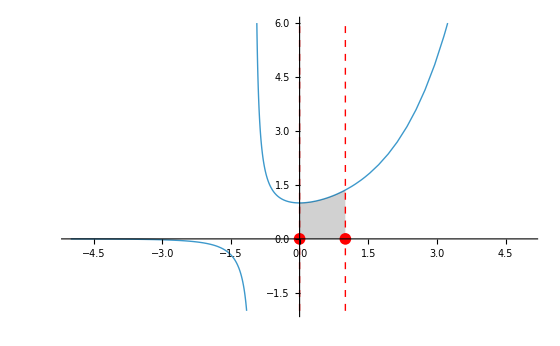

```mathematica
Show[pGlobal,Graphics[{{Opacity[.18],EdgeForm[None],fillUnder[f,{0,1}]},{Red,Thick,Dashed,Line[{{0,-2},{0,6}}],Line[{{1,-2},{1,6}}]},{Red,PointSize[0.015],Point[{0,0}],Point[{1,0}]}}]
]
```

La primitiva de f(x) no puede escribirse usando las funciones que hemos visto en el curso. Se obtiene usando la exponencial integral Ei(x), que se define como una función de área de e^x/x.

```mathematica
∫f[x]ⅆx
```

ExpIntegralEi[1+x]/ⅇ

El valor numérico exacto de la integral entre [0,1] es el siguiente

```mathematica
A:=∫_0^1 f[x]ⅆx; AN:=N[A,10]; {A,AN}
```

{(-ExpIntegralEi[1]+ExpIntegralEi[2])/ⅇ,1.125386083}

1. - Regla simple del rectángulo: aproximamos el área por un rectángulo de altura f(a).

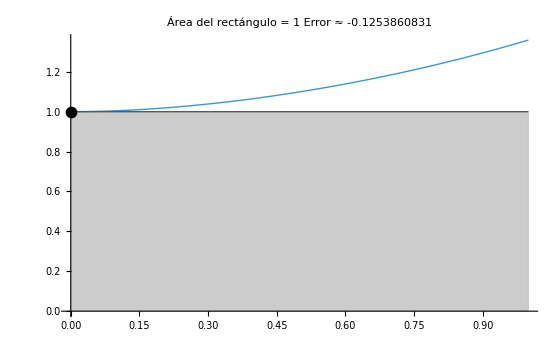

```mathematica
Q:=(b-a) f[a];
EE:=Q-A;
pR=Plot[f[x],{x,a,b},PlotStyle->Thick,PlotRange->All,AxesOrigin->{a,0},ImageSize->560];
rectPoly=Polygon[{{a,0},{b,0},{b,f[a]},{a,f[a]}}];
Show[pR,Graphics[{{Opacity[.20],EdgeForm[GrayLevel[.35]],rectPoly},{GrayLevel[.35],Thick,Line[{{a,f[a]},{b,f[a]}}]},{Black,PointSize[0.015],Point[{a,f[a]}]}}],PlotLabel->Row[{"Área del rectángulo = ",Q,"     Error ","  ≈  ",NumberForm[N[EE,10],{12,10}]}]]
gRect=%;
```

2. - Regla simple del punto medio: aproximamos el área por un rectángulo de altura f((a+b)/2).

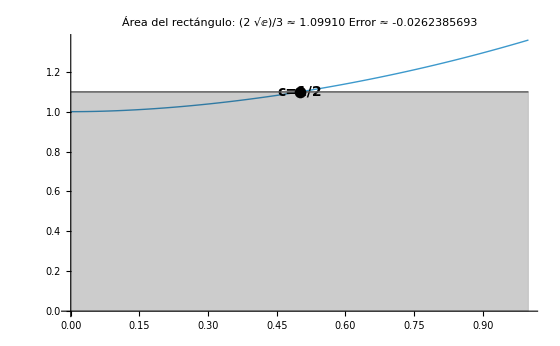

```mathematica
c=(a+b)/2;

QPM=(b-a) f[c]//FullSimplify;
EPM=QPM-A//FullSimplify;

pPM=Plot[f[x],{x,a,b},PlotStyle->Thick,PlotRange->All,AxesOrigin->{a,0},ImageSize->560];

midPoly=Polygon[{{a,0},{b,0},{b,f[c]},{a,f[c]}}];

Show[pPM,Graphics[{{Opacity[.20],EdgeForm[GrayLevel[.35]],midPoly},{GrayLevel[.35],Thick,Line[{{a,f[c]},{b,f[c]}}]},{Black,PointSize[0.015],Point[{c,f[c]}]},Text[Style["c=1/2",14,Bold,Black],{c,f[c]},{0,1.2}]
}],PlotLabel->Row[{"Área del rectángulo: ",QPM,"  ≈  ",NumberForm[N[QPM,5],{12,5}],"     Error ","  ≈  ",NumberForm[N[EPM,10],{12,10}]}]]
gPM=%;
```

3. - Regla simple del trapecio: aproximamos el área por un trapecio de alturas f(a) y f(b), cuyo área viene dada por 1/2*(f(a)+f(b))(b-a).

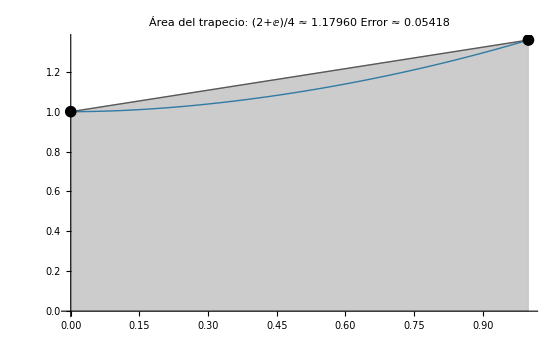

```mathematica
QT=(b-a)/2 (f[a]+f[b])//FullSimplify;
ET=QT-A//FullSimplify;

pT=Plot[f[x],{x,a,b},PlotStyle->Thick,PlotRange->All,AxesOrigin->{a,0},ImageSize->560];

trapPoly=Polygon[{{a,0},{b,0},{b,f[b]},{a,f[a]}}];

Show[pT,Graphics[{{Opacity[.20],EdgeForm[GrayLevel[.35]],trapPoly},{GrayLevel[.35],Thick,Line[{{a,f[a]},{b,f[b]}}]},{Black,PointSize[0.015],Point[{a,f[a]}],Point[{b,f[b]}]}}],PlotLabel->Row[{"Área del trapecio: ",QT,"  ≈  ",NumberForm[N[QT,5],{12,5}],"     Error ","  ≈  ",NumberForm[N[ET,20],{12,5}]}]]
gTrap=%;
```

4. - Regla simple de Simpson. Se calcula el área bajo el polinomio de segundo grado que pasa por (a,f(a)), (b,f(b)) y (c,f(c)).

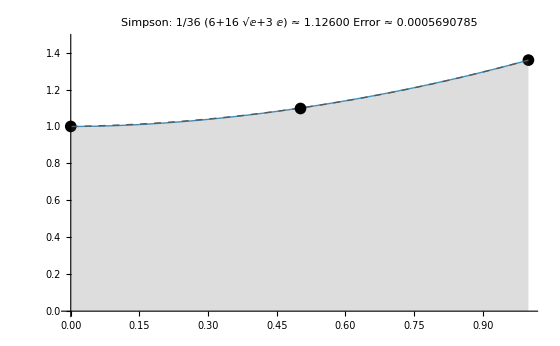

```mathematica
QS=(b-a)/6 (f[a]+4 f[c]+f[b])//FullSimplify;
ES=QS-A//FullSimplify;
p[x_]=InterpolatingPolynomial[{{a,f[a]},{c,f[c]},{b,f[b]}},x]//Expand;
yMax=1.08 Max[f/@Subdivide[a,b,300]];
pBase=Plot[f[x],{x,a,b},PlotStyle->Thick,PlotRange->{{a,b},{0,yMax}},AxesOrigin->{a,0},ImageSize->560];
pSim=Plot[p[x],{x,a,b},PlotStyle->{Thick,Dashed,GrayLevel[.35]},PlotRange->{{a,b},{0,yMax}},Filling->0,FillingStyle->Opacity[.20]];
Show[pBase,pSim,Graphics[{Black,PointSize[0.015],Point[{a,f[a]}],Point[{c,f[c]}],Point[{b,f[b]}]}],PlotLabel->Row[{"Simpson: ",QS,"  ≈  ",NumberForm[N[QS,5],{12,5}],"     Error ","  ≈  ",NumberForm[N[ES,20],{12,10}]}]]
gSimp=%;
```

Resumen de los resultados.

```mathematica
panel[g_,name_,err_]:=Labeled[Show[g,PlotLabel->None,ImageSize->420],Style[Row[{name,"   Error ≈  ",NumberForm[N[err,20],{12,10}]}],14],Top];

GraphicsGrid[{{panel[gRect,"Rectángulo.",EE],panel[gPM,"Punto medio.",EPM]},{panel[gTrap,"Trapecio.",ET],panel[gSimp,"Simpson.",ES]}},Spacings->{0.6,0.9}]
```

-Graphics-

```mathematica
ClearAll[quadCompositeGrid];

quadCompositeGrid[n_Integer?Positive]:=Module[{h,nodes,mids,exact,exactN,yMax,qR,qPM,qT,qS,eR,ePM,eT,eS,base,partLines,rectFill,midFill,trapFill,simpsonPolys,pPiece,simpsonPlot,gRect,gMid,gTrap,gSimp,panel,header},If[!ValueQ[A],A=Integrate[f[x],{x,a,b}]//FullSimplify];
exact=A;
exactN=N[exact,30];
h=(b-a)/n;
nodes=Subdivide[a,b,n];
mids=Most[nodes]+h/2;
yMax=1.08 Max[f/@Subdivide[a,b,400]];
base=Plot[f[x],{x,a,b},PlotStyle->Thick,PlotRange->{{a,b},{0,yMax}},AxesOrigin->{a,0},ImageSize->420];
partLines=Graphics[{GrayLevel[.85],AbsoluteThickness[1],Table[Line[{{xi,0},{xi,yMax}}],{xi,nodes}]}];
qR=h Total[f/@Most[nodes]];
eR=qR-exactN;
qPM=h Total[f/@mids];
ePM=qPM-exactN;
qT=h ((f[a]+f[b])/2+Total[f/@nodes[[2;;-2]]]);
eT=qT-exactN;
If[EvenQ[n],qS=(h/3) (f[a]+f[b]+4 Total[f/@nodes[[2;;-1;;2]]]+2 Total[f/@nodes[[3;;-2;;2]]]);
eS=qS-exactN;,qS=Missing["EvenNRequired"];
eS=Missing["EvenNRequired"];];
rectFill=Graphics[{Opacity[.20],EdgeForm[GrayLevel[.4]],Table[With[{xL=nodes[[i]],xR=nodes[[i+1]],hh=f[nodes[[i]]]},Polygon[{{xL,0},{xR,0},{xR,hh},{xL,hh}}]],{i,1,n}]}];
midFill=Graphics[{Opacity[.20],EdgeForm[GrayLevel[.4]],Table[With[{xL=nodes[[i]],xR=nodes[[i+1]],hh=f[(nodes[[i]]+nodes[[i+1]])/2]},Polygon[{{xL,0},{xR,0},{xR,hh},{xL,hh}}]],{i,1,n}]}];
trapFill=Graphics[{Opacity[.20],EdgeForm[GrayLevel[.4]],Table[With[{xL=nodes[[i]],xR=nodes[[i+1]],hL=f[nodes[[i]]],hR=f[nodes[[i+1]]]},Polygon[{{xL,0},{xR,0},{xR,hR},{xL,hL}}]],{i,1,n}]}];
If[EvenQ[n],simpsonPolys=Table[With[{x0=nodes[[2 k+1]],x1=nodes[[2 k+2]],x2=nodes[[2 k+3]]},InterpolatingPolynomial[{{x0,f[x0]},{x1,f[x1]},{x2,f[x2]}},x]],{k,0,n/2-1}];
pPiece[x_]:=Piecewise[Table[With[{xL=nodes[[2 k+1]],xR=nodes[[2 k+3]]},{simpsonPolys[[k+1]],xL<=x<=xR}],{k,0,n/2-1}],0];
simpsonPlot=Plot[pPiece[x],{x,a,b},PlotStyle->{Thick,Dashed,GrayLevel[.35]},PlotRange->{{a,b},{0,yMax}},Filling->0,FillingStyle->Opacity[.20],ImageSize->420];];
gRect=Show[base,rectFill,partLines];
gMid=Show[base,midFill,partLines];
gTrap=Show[base,trapFill,partLines];
gSimp=If[EvenQ[n],Show[base,simpsonPlot,partLines],Show[base,partLines,PlotLabel->Style["Simpson requiere n par",14,Red]]];
panel[g_,name_,q_,e_]:=Labeled[Show[g,PlotLabel->None,ImageSize->420],Style[If[MissingQ[q],Row[{name,"   (n debe ser par)"}],Row[{name,"   Aprox. ≈ ",NumberForm[N[q,20],{12,10}],"   |E| ≈ ",NumberForm[N[Abs[e],20],{12,8}]}]],14],Top];
header=Style[Row[{"Área exacta  ≈  ",NumberForm[exactN,{12,10}],"     (n = ",n,")"}],14,Bold];
Labeled[GraphicsGrid[{{panel[gRect,"Rectángulo comp.",qR,eR],panel[gMid,"Punto medio comp.",qPM,ePM]},{panel[gTrap,"Trapecio comp.",qT,eT],panel[gSimp,"Simpson comp.",qS,eS]}},Spacings->{0.6,0.9}],header,Top]];
```

Reglas compuestas; se divide el intervalo en n subintervalos y se aplica la regla de cuadratura en cada uno. Por simplicidad, tomamos los intervalos de igual longitud.

```mathematica
quadCompositeGrid[4]
```

-Graphics-